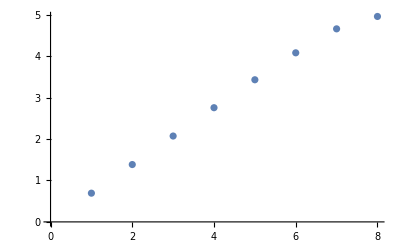

```mathematica
ListPlot[{0.693031864112,1.38382706399,2.0717512632,2.75527380927,3.42920734874,4.07945845292,4.65759494623,4.95657371291}]
```

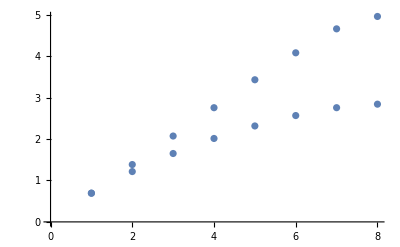

```mathematica
Show[ListPlot[{0.693031864112,1.38382706399,2.0717512632,2.75527380927,3.42920734874,4.07945845292,4.65759494623,4.95657371291}],ListPlot[{0.692868492617,1.21459238232,1.65006420879,2.01296483824,2.31465128042,2.56581867676,2.75556145816,2.84040178487}]]
```

```mathematica
NN=20
```

20

```mathematica
Scaling={};
```

```mathematica
Do[
SPage=Sum[1./k,{k,2^(NN-l)+1,2^NN}]-(2^l-1)/(2*2^(NN-l));
AppendTo[Scaling,SPage],
{l,1,10}]
```

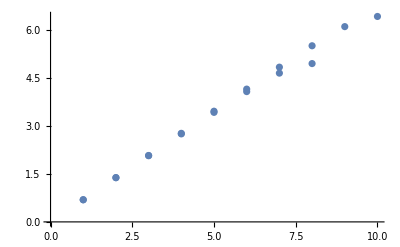

```mathematica
Show[ListPlot[Scaling],ListPlot[{0.693031864112,1.38382706399,2.0717512632,2.75527380927,3.42920734874,4.07945845292,4.65759494623,4.95657371291}]]
```

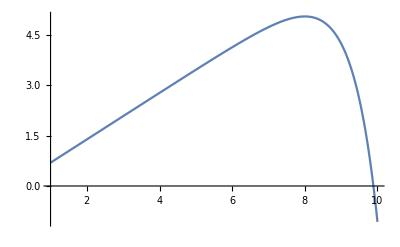

```mathematica
Plot[Log[2^l]-2^l/(2*2^(NN-l)),{l,1,10}]
```

```mathematica
Page={0.693146489914,1.38512455621,2.0753532972,2.76382094893,3.4502533589,4.13294437795,4.80826998751,5.46120123367,6.03984564572,6.34342692879}
```

{0.693146,1.38512,2.07535,2.76382,3.45025,4.13294,4.80827,5.4612,6.03985,6.34343}

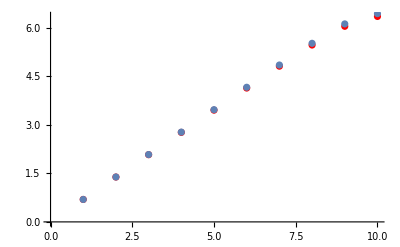

```mathematica
Show[ListPlot[Page,PlotStyle->Red],ListPlot[Scaling]]
```

```mathematica
PositiveState={0.693142294883728,1.2176068276166916,1.654742605984211,2.023103304207325,2.3361477851867676,2.6060592187568545,2.842615319881588,3.049069254891947}
```

{0.693142,1.21761,1.65474,2.0231,2.33615,2.60606,2.84262,3.04907}

```mathematica
SortedPositive={0.37929263710975647,0.7520899064838886,1.0080666153226048,1.1786837284744252,1.2956935678230366,1.3782089029461986,1.4367962634732976,1.4774400383894317}
```

{0.379293,0.75209,1.00807,1.17868,1.29569,1.37821,1.4368,1.47744}

```mathematica
Shuffled1={0.6930563449859619,1.069036740809679,1.3987468089908361,1.5710247294045985,1.7121641270350665,1.8074912423617207,1.8884591684909537,1.9345043037792493}
```

{0.693056,1.06904,1.39875,1.57102,1.71216,1.80749,1.88846,1.9345}

```mathematica
Shuffled4={0.5843187719583511,1.1499023139476776,1.5292647927999496,1.8132256902754307,2.0684751626104116,2.253149062395096,2.4569043496157974,2.5712090419838205,2.6317679360836337
}
```

{0.584319,1.1499,1.52926,1.81323,2.06848,2.25315,2.4569,2.57121,2.63177}

```mathematica
FullyRandom4={0.6930502653121948,1.1642466932535172,1.5321666449308395,2.0050345342606306,2.2289288877509534,2.4356919310521334,2.5815985477529466,2.7427954566373955}
```

{0.69305,1.16425,1.53217,2.00503,2.22893,2.43569,2.5816,2.7428}

```mathematica
ShallowRandom={0.6692125201225281,1.0615783743560314,1.3378637786954641,1.5190249462611973,1.643895902321674,1.7166792812058702,1.8197283584886463}
```

{0.669213,1.06158,1.33786,1.51902,1.6439,1.71668,1.81973}

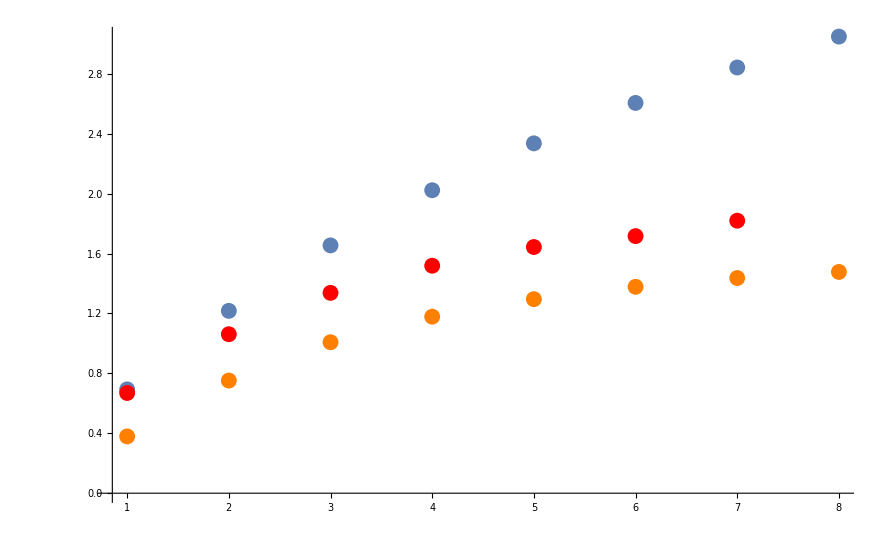

```mathematica
Show[ListPlot[PositiveState,PlotRange->All],ListPlot[ShallowRandom,PlotStyle->Red],ListPlot[SortedPositive,PlotStyle->Orange]]
```

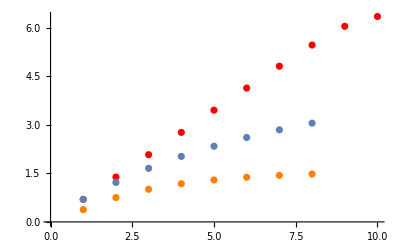

```mathematica
Show[ListPlot[Page,PlotStyle->Red],ListPlot[PositiveState],ListPlot[SortedPositive,PlotStyle->Orange]]
```

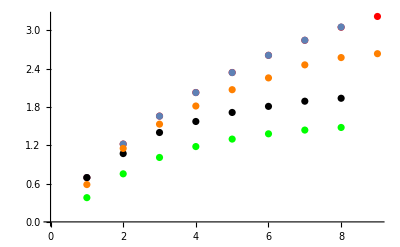

```mathematica
Show[ListPlot[ShallowRandom,PlotStyle->Red],ListPlot[PositiveState],ListPlot[SortedPositive,PlotStyle->Green],ListPlot[Shuffled1,PlotStyle->Black],ListPlot[Shuffled4,PlotStyle->Orange]]
```

```mathematica
Binomial[20,10]
```

184756

```mathematica
16*96+96
```

1632

```mathematica
Solve[16.*h+h^2+h==1632,h]
```

{{h→-49.7826},{h→32.7826}}